# Hitting of Cyclones to West Coast North America

Baoxiang Pan
7.10.2017

## Import Lagrangian Detected Cyclone Data

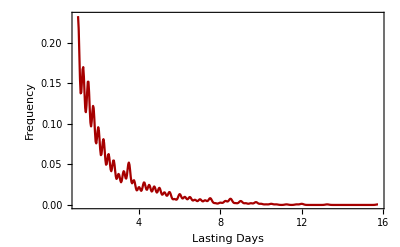

```mathematica
cyclones=Import["/Users/lambda/Documents/Data/Cyclones/ncepstorms_2009.txt","Table"];
data=Table[Select[cyclones,#[[-1]]==i&],{i,Max[Map[#[[-1]]&,cyclones]]}];
length=Map[Length,data]*0.25;
Block[{distribution=SmoothKernelDistribution[length]},
Plot[PDF[distribution, x], {x, 1, Max[length]},
	PlotRange->Full,
	BaseStyle->18,
	Frame->True,
	FrameLabel->{"Lasting Days","Frequency"}]]
```

```mathematica
ncepstorms_2012.txt
```

```mathematica
cyclones=Import["/Users/lambda/Documents/Data/Cyclones/cyclones.txt","Table"][[2;;]];
```

```mathematica
Table[Block[{filename="ncepstorms_19"<>ToString[i]<>".txt"},
	Export[filename,Select[cyclones,#[[3]]==i&],"Table"]],{i,58,99}];
```

```mathematica
Table[Block[{filename="ncepstorms_200"<>ToString[i]<>".txt"},
	Export[filename,Select[cyclones,#[[3]]==i&],"Table"]],{i,0,8}];
```

```mathematica
CycloneSpecify[time_,range_]:=Block[{file="ncepstorms_"<>ToString[time[[1]]]<>".txt",
			lag=10,cyclones,s1,s2,ByPass},
	SetDirectory["/Users/lambda/Documents/Data/Cyclones"];
	cyclones=Import[file,"Table"];
	s1=Select[cyclones,Abs[DateDifference[If[#[[3]]<20,
							DateObject[{2000+#[[3]],#[[4]],#[[5]]},"Day", "Gregorian", -6.],
							DateObject[{1900+#[[3]],#[[4]],#[[5]]},"Day", "Gregorian", -6.]],
							DateObject[time,"Day","Gregorian",-6.]][[1]]]<lag&];
	s2=Table[Select[s1,#[[-1]]==i&],{i,Max[Map[#[[-1]]&,s1]]}];
	ByPass[track_]:=Block[{InOrNot},
	    InOrNot[point_]:=And[point[[1]]>=range[[1,1]],point[[1]]<range[[1,2]],
	                       point[[2]]>=range[[2,1]],point[[2]]<range[[2,2]]];
		Map[InOrNot[{#[[14]],#[[15]]}]&,track]/.List->Or];
	Select[s2,ByPass]];
```

```mathematica
CycloneSpecify[{1969,1,1},{{20,60},{190,230}}]
```

{{{1.,1,69,1,1,0,15,1,1,994.13,9.72,-999.,-999.,33.31,193.17,13,31,0,0,1},{1.25,2,69,1,1,6,14,1,0,990.4,16.59,337.13,-3.73,35.13,196.11,14,30,0,0,1},{1.5,3,69,1,1,12,16,1,0,989.86,17.41,334.14,-0.54,36.78,199.23,15,29,0,0,1},{1.75,4,69,1,1,18,14,1,0,988.47,18.07,331.44,-1.38,38.23,202.52,16,28,0,0,1},{2.,5,69,1,2,0,17,1,0,982.78,21.54,269.55,-5.69,40.52,203.55,17,28,0,0,1},{2.25,6,69,1,2,6,19,1,0,984.53,25.92,267.05,1.74,42.78,204.68,18,28,0,0,1},{2.5,7,69,1,2,12,19,1,0,987.35,19.08,331.36,2.82,43.88,208.5,19,27,0,0,1},{2.75,8,69,1,2,18,15,1,0,986.92,22.98,543.56,-0.43,46.78,214.11,21,26,0,0,1},{3.,9,69,1,3,0,16,1,0,985.19,23.4,512.69,-1.73,50.68,217.88,23,26,0,0,1},{3.25,10,69,1,3,6,13,1,0,982.2,27.52,586.87,-2.99,55.87,219.56,25,27,0,0,1},{3.5,11,69,1,3,12,15,1,0,976.92,33.7,248.01,-5.28,57.32,216.47,25,28,0,0,1},{3.75,12,69,1,3,18,13,1,0,980.57,25.82,247.06,3.64,58.66,213.11,25,29,0,0,1},{4.,13,69,1,4,0,12,1,0,988.57,19.3,0.,8.01,58.66,213.11,25,29,0,0,1},{4.25,14,69,1,4,6,12,1,0,994.33,32.26,246.21,5.76,59.88,209.48,25,30,0,0,1},{4.5,15,69,1,4,12,16,1,0,999.85,9.83,246.21,5.52,58.66,213.11,25,29,0,0,1},{4.75,16,69,1,4,18,15,1,0,1000.46,10.,0.,0.61,58.66,213.11,25,29,0,0,1},{5.,17,69,1,5,0,16,1,0,999.99,15.64,341.5,-0.47,59.18,218.99,26,28,0,0,1},{5.25,18,69,1,5,6,17,1,0,1004.05,7.49,252.95,4.05,57.32,216.47,25,28,0,0,1},{5.5,19,69,1,5,12,15,1,0,1007.27,5.3,0.,3.23,57.32,216.47,25,28,0,0,1},{5.75,20,69,1,5,18,16,1,0,1007.81,8.93,0.,0.54,57.32,216.47,25,28,0,0,1},{6.,21,69,1,6,0,17,1,0,1006.19,10.98,0.,-1.61,57.32,216.47,25,28,0,0,1},{6.25,22,69,1,6,6,18,1,0,1005.42,5.89,248.01,-0.78,55.87,219.56,25,27,0,0,1},{6.5,23,69,1,6,12,19,1,0,1006.19,5.73,0.,0.78,55.87,219.56,25,27,0,0,1},{6.75,24,69,1,6,18,22,1,0,1003.18,9.75,538.42,-3.01,54.32,227.6,26,25,0,0,1},{7.,25,69,1,7,0,21,1,0,1001.06,16.02,0.,-2.12,54.32,227.6,26,25,0,0,1},{7.25,26,69,1,7,6,20,1,0,1001.65,18.45,0.,0.59,54.32,227.6,26,25,0,0,1},{7.5,27,69,1,7,12,17,1,0,1005.1,17.27,0.,3.45,54.32,227.6,26,25,0,1,1}},{{1.,1,69,1,1,0,15,1,1,1007.58,6.35,-999.,-999.,29.67,220.24,17,20,0,0,2},{1.25,2,69,1,1,6,14,1,0,1009.81,5.74,0.,2.23,29.67,220.24,17,20,0,0,2},{1.5,3,69,1,1,12,16,1,0,1011.11,3.84,0.,1.31,29.67,220.24,17,20,0,1,2}},{{1.,1,69,1,1,0,15,1,1,1001.57,15.85,-999.,-999.,47.56,227.2,24,23,0,0,4},{1.25,2,69,1,1,6,14,1,0,1005.92,11.98,0.,4.35,47.56,227.2,24,23,0,0,4},{1.5,3,69,1,1,12,16,1,0,1008.41,12.14,329.91,2.49,47.3,231.58,25,22,0,0,4},{1.75,4,69,1,1,18,14,1,0,1010.03,10.34,254.54,1.62,49.16,229.57,25,23,0,1,4}},{{1.,1,69,1,1,0,15,1,1,1005.41,28.63,-999.,-999.,59.18,218.99,26,28,0,0,5},{1.25,2,69,1,1,6,14,1,0,1000.75,30.86,0.,-4.66,59.18,218.99,26,28,0,0,5},{1.5,3,69,1,1,12,16,1,0,1002.88,25.3,0.,2.13,59.18,218.99,26,28,0,0,5},{1.75,4,69,1,1,18,14,1,0,1002.51,21.24,341.5,-0.37,58.66,213.11,25,29,0,0,5},{2.,5,69,1,2,0,17,1,0,1003.73,17.57,0.,1.22,58.66,213.11,25,29,0,0,5},{2.25,6,69,1,2,6,19,1,0,1000.73,18.41,0.,-3.,58.66,213.11,25,29,0,0,5},{2.5,7,69,1,2,12,19,1,0,1002.99,14.53,0.,2.25,58.66,213.11,25,29,0,0,5},{2.75,8,69,1,2,18,15,1,0,999.07,16.14,0.,-3.91,58.66,213.11,25,29,0,1,5}},{{2.25,6,69,1,2,6,19,1,0,1002.33,7.34,-999.,-999.,27.65,194.3,11,30,1,1,30}},{{3.25,10,69,1,3,6,13,1,0,1006.71,5.86,-999.,-999.,29.16,204.08,13,26,1,0,44},{3.5,11,69,1,3,12,15,1,0,1008.2,5.04,321.83,1.48,27.75,201.19,12,27,0,0,44},{3.75,12,69,1,3,18,13,1,0,1010.69,6.98,640.67,2.49,30.38,207.07,14,25,0,1,44}},{{5.75,20,69,1,5,18,16,1,0,1003.33,5.94,-999.,-999.,21.78,201.62,10,26,1,0,76},{6.,21,69,1,6,0,17,1,0,999.9,6.79,0.,-3.44,21.78,201.62,10,26,0,0,76},{6.25,22,69,1,6,6,18,1,0,999.48,11.96,288.8,-0.42,24.29,202.38,11,26,0,0,76},{6.5,23,69,1,6,12,19,1,0,997.98,12.05,0.,-1.49,24.29,202.38,11,26,0,0,76},{6.75,24,69,1,6,18,22,1,0,998.07,14.25,284.7,0.09,26.75,203.2,12,26,0,0,76},{7.,25,69,1,7,0,21,1,0,996.58,13.32,0.,-1.49,26.75,203.2,12,26,0,0,76},{7.25,26,69,1,7,6,20,1,0,999.43,9.14,0.,2.85,26.75,203.2,12,26,0,0,76},{7.5,27,69,1,7,12,17,1,0,999.78,10.98,226.63,0.36,27.75,201.19,12,27,0,0,76},{7.75,28,69,1,7,18,20,1,0,1001.64,8.23,0.,1.86,27.75,201.19,12,27,0,0,76},{8.,29,69,1,8,0,21,1,0,1001.45,7.2,225.1,-0.19,28.65,199.13,12,28,0,0,76},{8.25,30,69,1,8,6,22,1,0,1003.47,7.01,223.84,2.02,29.46,197.02,12,29,0,0,76},{8.5,31,69,1,8,12,22,1,0,1003.63,5.64,0.,0.16,29.46,197.02,12,29,0,0,76},{8.75,32,69,1,8,18,19,1,0,1003.19,8.37,222.74,-0.44,30.18,194.86,12,30,0,0,76},{9.,33,69,1,9,0,19,1,0,1003.51,6.68,0.,0.32,30.18,194.86,12,30,0,0,76},{9.25,34,69,1,9,6,24,1,0,1004.41,7.63,221.75,0.89,30.8,192.65,12,31,0,0,76},{9.5,35,69,1,9,12,20,1,0,1005.34,5.2,286.53,0.93,28.25,192.17,11,31,0,0,76},{9.75,36,69,1,9,18,18,1,0,1005.42,5.05,219.11,0.09,27.65,194.3,11,30,0,0,76},{10.,37,69,1,10,0,16,1,0,1004.11,5.69,0.,-1.31,27.65,194.3,11,30,0,1,76}},{{8.,29,69,1,8,0,21,1,0,1011.71,10.99,-999.,-999.,59.18,218.99,26,28,1,0,112},{8.25,30,69,1,8,6,22,1,0,1009.85,10.8,248.08,-1.87,60.59,215.54,26,29,0,0,112},{8.5,31,69,1,8,12,22,1,0,1007.52,12.12,573.54,-2.32,55.87,219.56,25,27,0,0,112},{8.75,32,69,1,8,18,19,1,0,1002.84,15.91,248.99,-4.68,54.32,222.4,25,26,0,0,112},{9.,33,69,1,9,0,19,1,0,997.84,22.63,250.23,-5.,52.68,225.,25,25,0,0,112},{9.25,34,69,1,9,6,24,1,0,993.95,27.74,335.18,-3.89,52.54,229.97,26,24,0,0,112},{9.5,35,69,1,9,12,20,1,0,993.87,20.22,0.,-0.08,52.54,229.97,26,24,0,0,112},{9.75,36,69,1,9,18,18,1,0,991.14,15.14,335.18,-2.73,52.68,225.,25,25,0,0,112},{10.,37,69,1,10,0,16,1,0,987.6,19.16,0.,-3.54,52.68,225.,25,25,0,0,112},{10.25,38,69,1,10,6,16,1,0,985.84,13.9,251.51,-1.75,50.96,227.39,25,24,0,0,112},{10.5,39,69,1,10,12,18,1,0,984.25,17.83,0.,-1.59,50.96,227.39,25,24,0,0,112},{10.75,40,69,1,10,18,21,1,0,983.19,20.08,252.95,-1.06,49.16,229.57,25,23,0,0,112}},{{9.,33,69,1,9,0,19,1,0,1008.4,16.2,-999.,-999.,34.91,209.29,16,25,1,0,124},{9.25,34,69,1,9,6,24,1,0,1009.59,11.92,0.,1.19,34.91,209.29,16,25,0,0,124},{9.5,35,69,1,9,12,20,1,0,1009.04,9.08,0.,-0.54,34.91,209.29,16,25,0,1,124}},{{10.25,38,69,1,10,6,16,1,0,1004.03,4.78,-999.,-999.,28.05,206.07,13,25,1,0,146},{10.5,39,69,1,10,12,18,1,0,1001.73,4.7,315.37,-2.31,29.16,209.05,14,24,0,0,146},{10.75,40,69,1,10,18,21,1,0,1001.37,6.98,313.14,-0.35,30.08,212.12,15,23,0,0,146}}}

```mathematica
tempt=%;
```

```mathematica
tempt[[4]]
```

{{1.,1,69,1,1,0,15,1,1,1001.57,15.85,-999.,-999.,47.56,227.2,24,23,0,0,4},{1.25,2,69,1,1,6,14,1,0,1005.92,11.98,0.,4.35,47.56,227.2,24,23,0,0,4},{1.5,3,69,1,1,12,16,1,0,1008.41,12.14,329.91,2.49,47.3,231.58,25,22,0,0,4},{1.75,4,69,1,1,18,14,1,0,1010.03,10.34,254.54,1.62,49.16,229.57,25,23,0,1,4}}

```mathematica
Map[Length,tempt]
```

{27,3,4,8,1,3,18,12,3,3}